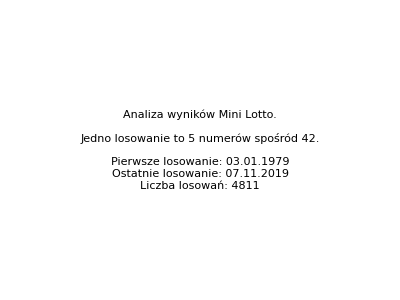

```mathematica
dane = Import["http://mbnet.com.pl/el.xls","Data"];
dane = Flatten[dane,1];
daty = Take[#,{2}]&/@dane;
pierwsze = daty[[1]];
ostatnie =daty[[Length[daty]]];
ilosc = Length[dane];
daty2 = Last[#]&/@daty ;
wylos = IntegerPart[Drop[#,2]&/@dane];
wylos2 = Sort[Last[#]&/@wylos ];

czescA = Graphics[Text[Style[StringJoin["Analiza wyników Mini Lotto.\n\nJedno losowanie to 5 numerów spośród 42.\n\nPierwsze losowanie: ",pierwsze,"\nOstatnie losowanie: ",ostatnie,
"\nLiczba losowań: ",ToString[ilosc]],Medium]]]
```

```mathematica
Tally[wylos2];
pary = Flatten[Table[Subsets[wylos[[i]],{2}],{i, 1, Length[wylos]}],1];
liczbapar = Tally[pary];
r = ReverseSortBy[liczbapar,Last][[1;;12]];
rr = Last[#]&/@r;
dwojki = First[#]&/@r;
lab=Table[Rotate[GraphicsRow[{
Graphics[{RGBColor["#F6D187"],Disk[],Black,
Rotate[Text[r[[i,1]][[1]]],270 Degree]},ImageSize->60],
Graphics[{RGBColor["#F6D187"],Disk[],Black,
Rotate[Text[r[[i,1]][[2]]],270 Degree]}]},ImageSize->60],
90 Degree],{i,1,12}];

czescB=Labeled[Framed[BarChart[rr, ImageSize->400,ColorFunction->ColorData["LightTerrain"],
PlotRange->{Automatic,{0,120}},
ChartLabels ->Placed[{lab,rr},{Above,Center}]],
RoundingRadius->10],Framed["Najczęściej losowane pary liczb:",RoundingRadius->10],Top]
```

-Graphics-Najczęściej losowane pary liczb:

```mathematica
trojki = Flatten[Table[Subsets[wylos[[i]],{3}],{i, 1, Length[wylos]}],1];
tally = Tally[trojki];
trzy = ReverseSortBy[tally,Last][[1;;12]];
rrr= Last[#]&/@trzy;
trojeczki = First[#]&/@trzy;
ab=Table[GraphicsRow[{
Graphics[{RGBColor["#F6D187"],Disk[],Black,
Text[trojeczki[[i]][[1]]]},ImageSize->60],
Graphics[{RGBColor["#F6D187"],Disk[],Black,
Text[trojeczki[[i]][[2]]]},ImageSize->60],
Graphics[{RGBColor["#F6D187"],Disk[],Black,
Text[trojeczki[[i]][[3]]]}]},ImageSize->60],
{i,1,12}];

czescC=BarChart[rrr,ImageSize->450,
PlotLabel -> Framed["Najczęściej losowane trójki liczb"],
PlotRange->{{0,15},Automatic},
BarOrigin->Left,ColorFunction->ColorData["ArmyColors"],
ChartLabels->Placed[{rrr, ab},{Center,After}],LabelingSize->60]
```

-Graphics-

```mathematica
kolo =ReverseSortBy[Tally[Table[Sort[Tally[EvenQ[wylos[[i]]]]],{i, 1, Length[wylos]}]]
/.{True->P,False->NP},Last];
ilePileNP = kolo[[All,2]];
ile=Flatten[Join[Table[{StringJoin[StringRiffle[kolo[[i,1]][[1]]],", ",
StringRiffle[kolo[[i,1]][[2]]]]},{i,1,4}],
Table[StringRiffle[kolo[[i,1]][[1]]],{i,5,6}]]];
wartosci = Table[Interpreter["Percent"][N[100*ilePileNP[[i]]/Total[ilePileNP],3]],
{i,1,6}];

czescD = PieChart[ilePileNP,ImageSize->450, ColorFunction->ColorData["LightTerrain"],
PlotLabel -> Framed["Częstość parzystych(P) i nieparzystych(NP) liczb w losowaniu."],
ChartLabels -> {Placed[{ile,wartosci},{"VerticalCallout","RadialCenter"}]},
SectorOrigin -> {Automatic,0.8}]
```

-Graphics-

```mathematica
calosc = Graphics[GraphicsGrid[{{czescA,czescB},{czescC,czescD}},
Background->{{RGBColor["#f5eee0"],White},{White,RGBColor["#f5eee0"]}},
Dividers->{{2->RGBColor["#f3d997"]},{2->RGBColor["#f3d997"]}}]];

CloudExport[calosc,"PDF","minilotto.pdf"]
```

CloudObject[https://www.wolframcloud.com/obj/wysieckaola/minilotto.pdf]